# 隣接行列とそのEigen

元データをランダムに作成

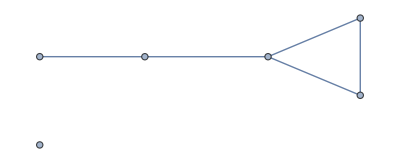

```mathematica
RandomGraph[{6,5}]
```

グラフを修正して2グループに分かれるように

```mathematica
m={{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,0,0,0},{0,0,0,0,1,1},{0,1,0,0,0,0}}
```

{{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,0,0,0},{0,0,0,0,1,1},{0,1,0,0,0,0}}

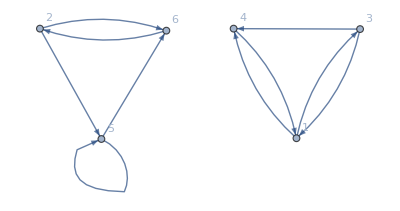

```mathematica
g=AdjacencyGraph[m,VertexLabels->Automatic]
```

固有ベクトルを座標とした場合、リンクが強いグループが近くなるはず。

```mathematica
ev=Eigenvectors[m]
```

{{0,1/2 (1+√5),0,0,1/2 (1+√5),1},{1/2 (1+√5),0,1/2 (1+√5),1,0,0},{-1,0,0,1,0,0},{0,1/2 (1-√5),0,0,1/2 (1-√5),1},{1/2 (1-√5),0,1/2 (1-√5),1,0,0},{0,0,0,0,-1,1}}

固有ベクトルをTransposeすると座標になる：

```mathematica
ep=Transpose[ev]
```

{{0,1/2 (1+√5),-1,0,1/2 (1-√5),0},{1/2 (1+√5),0,0,1/2 (1-√5),0,0},{0,1/2 (1+√5),0,0,1/2 (1-√5),0},{0,1,1,0,1,0},{1/2 (1+√5),0,0,1/2 (1-√5),0,-1},{1,0,0,1,0,1}}

```mathematica
ep2=Map[#[[1;;2]]&,ep]//N
```

{{0.,1.61803},{1.61803,0.},{0.,1.61803},{0.,1.},{1.61803,0.},{1.,0.}}

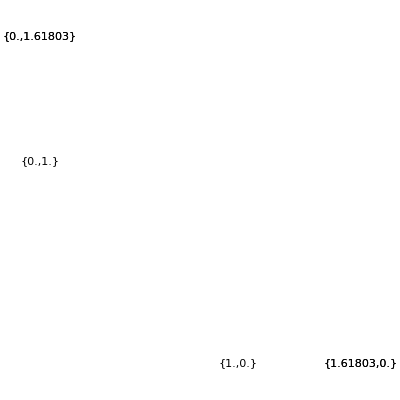

```mathematica
Graphics[MapIndexed[Text[#,#]&,ep2]]
```

```mathematica
Graphics[MapIndexed[Text[#2,#]&,ep2]]
```

-Graphics-

## 参考

GNN/GCN

https://qiita.com/omiita/items/429136c2f4e228d745ed

https://github.com/omiita/PyTorchGeometric-Tutorial/blob/master/PyTorch_Geometric_Tutorial.ipynb

(base) uname -a
Linux localhost.localdomain 3.10.0-1160.83.1.el7.x86_64 #1 SMP Wed Jan 25 16:41:43 UTC 2023 x86_64 x86_64 x86_64 GNU/Linux
(base) pip --version
pip 22.2.2 from /home/amano/miniconda3/lib/python3.9/site-packages/pip (python 3.9)
(base) pip install torch
Collecting torch
  Downloading torch-2.0.1-cp39-cp39-manylinux1_x86_64.whl (619.9 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 619.9/619.9 MB 358.5 kB/s eta 0:00:00
Collecting nvidia-cudnn-cu11==8.5.0.96
  Downloading nvidia_cudnn_cu11-8.5.0.96-2-py3-none-manylinux1_x86_64.whl (557.1 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 557.1/557.1 MB 415.4 kB/s eta 0:00:00
Collecting nvidia-cusolver-cu11==11.4.0.1
  Downloading nvidia_cusolver_cu11-11.4.0.1-2-py3-none-manylinux1_x86_64.whl (102.6 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 102.6/102.6 MB 2.8 MB/s eta 0:00:00
Collecting sympy
  Downloading sympy-1.12-py3-none-any.whl (5.7 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 5.7/5.7 MB 9.9 MB/s eta 0:00:00
Requirement already satisfied: typing-extensions in ./miniconda3/lib/python3.9/site-packages (from torch) (4.3.0)
Collecting nvidia-cuda-runtime-cu11==11.7.99
  Downloading nvidia_cuda_runtime_cu11-11.7.99-py3-none-manylinux1_x86_64.whl (849 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 849.3/849.3 kB 8.6 MB/s eta 0:00:00
Collecting nvidia-cublas-cu11==11.10.3.66
  Downloading nvidia_cublas_cu11-11.10.3.66-py3-none-manylinux1_x86_64.whl (317.1 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 317.1/317.1 MB 559.1 kB/s eta 0:00:00
Collecting filelock
  Downloading filelock-3.12.0-py3-none-any.whl (10 kB)
Collecting nvidia-curand-cu11==10.2.10.91
  Downloading nvidia_curand_cu11-10.2.10.91-py3-none-manylinux1_x86_64.whl (54.6 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 54.6/54.6 MB 4.7 MB/s eta 0:00:00
Collecting nvidia-nvtx-cu11==11.7.91
  Downloading nvidia_nvtx_cu11-11.7.91-py3-none-manylinux1_x86_64.whl (98 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 98.6/98.6 kB 11.9 MB/s eta 0:00:00
Collecting triton==2.0.0
  Downloading triton-2.0.0-1-cp39-cp39-manylinux2014_x86_64.manylinux_2_17_x86_64.whl (63.3 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 63.3/63.3 MB 4.4 MB/s eta 0:00:00
Collecting networkx
  Downloading networkx-3.1-py3-none-any.whl (2.1 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 2.1/2.1 MB 10.2 MB/s eta 0:00:00
Requirement already satisfied: jinja2 in ./miniconda3/lib/python3.9/site-packages (from torch) (3.1.2)
Collecting nvidia-nccl-cu11==2.14.3
  Downloading nvidia_nccl_cu11-2.14.3-py3-none-manylinux1_x86_64.whl (177.1 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 177.1/177.1 MB 1.1 MB/s eta 0:00:00
Collecting nvidia-cuda-cupti-cu11==11.7.101
  Downloading nvidia_cuda_cupti_cu11-11.7.101-py3-none-manylinux1_x86_64.whl (11.8 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 11.8/11.8 MB 9.7 MB/s eta 0:00:00
Collecting nvidia-cusparse-cu11==11.7.4.91
  Downloading nvidia_cusparse_cu11-11.7.4.91-py3-none-manylinux1_x86_64.whl (173.2 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 173.2/173.2 MB 2.0 MB/s eta 0:00:00
Collecting nvidia-cuda-nvrtc-cu11==11.7.99
  Downloading nvidia_cuda_nvrtc_cu11-11.7.99-2-py3-none-manylinux1_x86_64.whl (21.0 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 21.0/21.0 MB 8.1 MB/s eta 0:00:00
Collecting nvidia-cufft-cu11==10.9.0.58
  Downloading nvidia_cufft_cu11-10.9.0.58-py3-none-manylinux1_x86_64.whl (168.4 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 168.4/168.4 MB 1.7 MB/s eta 0:00:00
Requirement already satisfied: wheel in ./miniconda3/lib/python3.9/site-packages (from nvidia-cublas-cu11==11.10.3.66->torch) (0.37.1)
Requirement already satisfied: setuptools in ./miniconda3/lib/python3.9/site-packages (from nvidia-cublas-cu11==11.10.3.66->torch) (65.5.0)
Collecting cmake
  Downloading cmake-3.26.3-py2.py3-none-manylinux2014_x86_64.manylinux_2_17_x86_64.whl (24.0 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 24.0/24.0 MB 7.2 MB/s eta 0:00:00
Collecting lit
  Downloading lit-16.0.5.tar.gz (138 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 138.0/138.0 kB 10.7 MB/s eta 0:00:00
  Preparing metadata (setup.py) ... done
Requirement already satisfied: MarkupSafe>=2.0 in ./miniconda3/lib/python3.9/site-packages (from jinja2->torch) (2.1.1)
Collecting mpmath>=0.19
  Downloading mpmath-1.3.0-py3-none-any.whl (536 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 536.2/536.2 kB 8.9 MB/s eta 0:00:00
Building wheels for collected packages: lit
  Building wheel for lit (setup.py) ... done
  Created wheel for lit: filename=lit-16.0.5-py3-none-any.whl size=88177 sha256=715ecabc8630099cd2892f4d565726226c00392658288fb537183cb020e012f4
  Stored in directory: /home/amano/.cache/pip/wheels/d8/3a/a1/643264c1075b22759205027b760e0b1e85d975bfb333eef328
Successfully built lit
Installing collected packages: mpmath, lit, cmake, sympy, nvidia-nvtx-cu11, nvidia-nccl-cu11, nvidia-cusparse-cu11, nvidia-curand-cu11, nvidia-cufft-cu11, nvidia-cuda-runtime-cu11, nvidia-cuda-nvrtc-cu11, nvidia-cuda-cupti-cu11, nvidia-cublas-cu11, networkx, filelock, nvidia-cusolver-cu11, nvidia-cudnn-cu11, triton, torch
Successfully installed cmake-3.26.3 filelock-3.12.0 lit-16.0.5 mpmath-1.3.0 networkx-3.1 nvidia-cublas-cu11-11.10.3.66 nvidia-cuda-cupti-cu11-11.7.101 nvidia-cuda-nvrtc-cu11-11.7.99 nvidia-cuda-runtime-cu11-11.7.99 nvidia-cudnn-cu11-8.5.0.96 nvidia-cufft-cu11-10.9.0.58 nvidia-curand-cu11-10.2.10.91 nvidia-cusolver-cu11-11.4.0.1 nvidia-cusparse-cu11-11.7.4.91 nvidia-nccl-cu11-2.14.3 nvidia-nvtx-cu11-11.7.91 sympy-1.12 torch-2.0.1 triton-2.0.0
(base) python 
Python 3.9.13 (main, Oct 13 2022, 21:15:33) 
[GCC 11.2.0] :: Anaconda, Inc. on linux
Type “help”, “copyright”, “credits” or “license” for more information.
>>> import torch; print(torch.__version__)
2.0.1+cu117
>>> quit()
(base) pip install --verbose --no-cache-dir torch-scatter
Using pip 22.2.2 from /home/amano/miniconda3/lib/python3.9/site-packages/pip (python 3.9)
Collecting torch-scatter
  Downloading torch_scatter-2.1.1.tar.gz (107 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 107.6/107.6 kB 11.2 MB/s eta 0:00:00
  Running command python setup.py egg_info
  running egg_info
  creating /tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info
  writing /tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/PKG-INFO
  writing dependency_links to /tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/dependency_links.txt
  writing requirements to /tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/requires.txt
  writing top-level names to /tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/top_level.txt
  writing manifest file ‘/tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/SOURCES.txt’
  reading manifest file ‘/tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/SOURCES.txt’
  reading manifest template ‘MANIFEST.in’
  warning: no previously-included files matching ‘*’ found under directory ‘test’
  adding license file ‘LICENSE’
  writing manifest file ‘/tmp/pip-pip-egg-info-ddh0e2ov/torch_scatter.egg-info/SOURCES.txt’
  Preparing metadata (setup.py) ... done
Building wheels for collected packages: torch-scatter
  Running command python setup.py bdist_wheel
  running bdist_wheel
  running build
  running build_py
  creating build
  creating build/lib.linux-x86_64-cpython-39
  creating build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/__init__.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/placeholder.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/scatter.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/segment_coo.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/segment_csr.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/testing.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  copying torch_scatter/utils.py -> build/lib.linux-x86_64-cpython-39/torch_scatter
  creating build/lib.linux-x86_64-cpython-39/torch_scatter/composite
  copying torch_scatter/composite/__init__.py -> build/lib.linux-x86_64-cpython-39/torch_scatter/composite
  copying torch_scatter/composite/logsumexp.py -> build/lib.linux-x86_64-cpython-39/torch_scatter/composite
  copying torch_scatter/composite/softmax.py -> build/lib.linux-x86_64-cpython-39/torch_scatter/composite
  copying torch_scatter/composite/std.py -> build/lib.linux-x86_64-cpython-39/torch_scatter/composite
  running egg_info
  writing torch_scatter.egg-info/PKG-INFO
  writing dependency_links to torch_scatter.egg-info/dependency_links.txt
  writing requirements to torch_scatter.egg-info/requires.txt
  writing top-level names to torch_scatter.egg-info/top_level.txt
  reading manifest file ‘torch_scatter.egg-info/SOURCES.txt’
  reading manifest template ‘MANIFEST.in’
  warning: no previously-included files matching ‘*’ found under directory ‘test’
  adding license file ‘LICENSE’
  writing manifest file ‘torch_scatter.egg-info/SOURCES.txt’
  running build_ext
  building ‘torch_scatter._scatter_cpu’ extension
  creating build/temp.linux-x86_64-cpython-39
  creating build/temp.linux-x86_64-cpython-39/csrc
  creating build/temp.linux-x86_64-cpython-39/csrc/cpu
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/scatter_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/scatter_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_scatter_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/scatter.cpp -o build/temp.linux-x86_64-cpython-39/csrc/scatter.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_scatter_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/scatter_cpu.o build/temp.linux-x86_64-cpython-39/csrc/scatter.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_scatter/_scatter_cpu.so -s
  building ‘torch_scatter._segment_coo_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/segment_coo_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/segment_coo_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_segment_coo_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/segment_coo.cpp -o build/temp.linux-x86_64-cpython-39/csrc/segment_coo.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_segment_coo_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/segment_coo_cpu.o build/temp.linux-x86_64-cpython-39/csrc/segment_coo.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_scatter/_segment_coo_cpu.so -s
  building ‘torch_scatter._segment_csr_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/segment_csr_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/segment_csr_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_segment_csr_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/segment_csr.cpp -o build/temp.linux-x86_64-cpython-39/csrc/segment_csr.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_segment_csr_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/segment_csr_cpu.o build/temp.linux-x86_64-cpython-39/csrc/segment_csr.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_scatter/_segment_csr_cpu.so -s
  building ‘torch_scatter._version_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/version.cpp -o build/temp.linux-x86_64-cpython-39/csrc/version.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_version_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/version.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_scatter/_version_cpu.so -s
  /home/amano/miniconda3/lib/python3.9/site-packages/setuptools/command/install.py:34: SetuptoolsDeprecationWarning: setup.py install is deprecated. Use build and pip and other standards-based tools.
    warnings.warn(
  installing to build/bdist.linux-x86_64/wheel
  running install
  running install_lib
  creating build/bdist.linux-x86_64
  creating build/bdist.linux-x86_64/wheel
  creating build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/__init__.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/placeholder.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/scatter.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/segment_coo.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/segment_csr.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/testing.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/utils.py -> build/bdist.linux-x86_64/wheel/torch_scatter
  creating build/bdist.linux-x86_64/wheel/torch_scatter/composite
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/composite/__init__.py -> build/bdist.linux-x86_64/wheel/torch_scatter/composite
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/composite/logsumexp.py -> build/bdist.linux-x86_64/wheel/torch_scatter/composite
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/composite/softmax.py -> build/bdist.linux-x86_64/wheel/torch_scatter/composite
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/composite/std.py -> build/bdist.linux-x86_64/wheel/torch_scatter/composite
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/_scatter_cpu.so -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/_segment_coo_cpu.so -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/_segment_csr_cpu.so -> build/bdist.linux-x86_64/wheel/torch_scatter
  copying build/lib.linux-x86_64-cpython-39/torch_scatter/_version_cpu.so -> build/bdist.linux-x86_64/wheel/torch_scatter
  running install_egg_info
  Copying torch_scatter.egg-info to build/bdist.linux-x86_64/wheel/torch_scatter-2.1.1-py3.9.egg-info
  running install_scripts
  adding license file “LICENSE” (matched pattern “LICEN[CS]E*”)
  creating build/bdist.linux-x86_64/wheel/torch_scatter-2.1.1.dist-info/WHEEL
  creating ‘/tmp/pip-wheel-lr4ogji8/torch_scatter-2.1.1-cp39-cp39-linux_x86_64.whl’ and adding ‘build/bdist.linux-x86_64/wheel’ to it
  adding ‘torch_scatter/__init__.py’
  adding ‘torch_scatter/_scatter_cpu.so’
  adding ‘torch_scatter/_segment_coo_cpu.so’
  adding ‘torch_scatter/_segment_csr_cpu.so’
  adding ‘torch_scatter/_version_cpu.so’
  adding ‘torch_scatter/placeholder.py’
  adding ‘torch_scatter/scatter.py’
  adding ‘torch_scatter/segment_coo.py’
  adding ‘torch_scatter/segment_csr.py’
  adding ‘torch_scatter/testing.py’
  adding ‘torch_scatter/utils.py’
  adding ‘torch_scatter/composite/__init__.py’
  adding ‘torch_scatter/composite/logsumexp.py’
  adding ‘torch_scatter/composite/softmax.py’
  adding ‘torch_scatter/composite/std.py’
  adding ‘torch_scatter-2.1.1.dist-info/LICENSE’
  adding ‘torch_scatter-2.1.1.dist-info/METADATA’
  adding ‘torch_scatter-2.1.1.dist-info/WHEEL’
  adding ‘torch_scatter-2.1.1.dist-info/top_level.txt’
  adding ‘torch_scatter-2.1.1.dist-info/RECORD’
  removing build/bdist.linux-x86_64/wheel
  Building wheel for torch-scatter (setup.py) ... done
  Created wheel for torch-scatter: filename=torch_scatter-2.1.1-cp39-cp39-linux_x86_64.whl size=518188 sha256=a460f9f8c853e3c341660a8e5b9f5da0333802c9eae26072cdc2c3ac5eaa6e48
  Stored in directory: /tmp/pip-ephem-wheel-cache-vune0821/wheels/d5/0c/18/11b4cf31446c5d460543b0fff930fcac3a3f8a785e5c73fb15
Successfully built torch-scatter
Installing collected packages: torch-scatter
Successfully installed torch-scatter-2.1.1
(base) pip install --verbose --no-cache-dir torch-sparse
Using pip 22.2.2 from /home/amano/miniconda3/lib/python3.9/site-packages/pip (python 3.9)
Collecting torch-sparse
  Downloading torch_sparse-0.6.17.tar.gz (209 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 209.2/209.2 kB 10.0 MB/s eta 0:00:00
  Running command python setup.py egg_info
  running egg_info
  creating /tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info
  writing /tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/PKG-INFO
  writing dependency_links to /tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/dependency_links.txt
  writing requirements to /tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/requires.txt
  writing top-level names to /tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/top_level.txt
  writing manifest file ‘/tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/SOURCES.txt’
  reading manifest file ‘/tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/SOURCES.txt’
  reading manifest template ‘MANIFEST.in’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/css’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/html’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/tests’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/examples’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/benchmark’
  warning: no previously-included files matching ‘*’ found under directory ‘test’
  warning: no previously-included files matching ‘*’ found under directory ‘benchmark’
  adding license file ‘LICENSE’
  writing manifest file ‘/tmp/pip-pip-egg-info-mwofgy8c/torch_sparse.egg-info/SOURCES.txt’
  Preparing metadata (setup.py) ... done
Collecting scipy
  Downloading scipy-1.10.1-cp39-cp39-manylinux_2_17_x86_64.manylinux2014_x86_64.whl (34.5 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 34.5/34.5 MB 10.6 MB/s eta 0:00:00
Collecting numpy<1.27.0,>=1.19.5
  Downloading numpy-1.24.3-cp39-cp39-manylinux_2_17_x86_64.manylinux2014_x86_64.whl (17.3 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 17.3/17.3 MB 11.1 MB/s eta 0:00:00
Building wheels for collected packages: torch-sparse
  Running command python setup.py bdist_wheel
  running bdist_wheel
  running build
  running build_py
  creating build
  creating build/lib.linux-x86_64-cpython-39
  creating build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/__init__.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/add.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/bandwidth.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/cat.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/coalesce.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/convert.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/diag.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/eye.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/index_select.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/masked_select.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/matmul.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/metis.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/mul.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/narrow.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/permute.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/reduce.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/rw.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/saint.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/sample.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/select.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/spadd.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/spmm.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/spspmm.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/storage.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/tensor.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/testing.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/transpose.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/typing.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  copying torch_sparse/utils.py -> build/lib.linux-x86_64-cpython-39/torch_sparse
  running egg_info
  writing torch_sparse.egg-info/PKG-INFO
  writing dependency_links to torch_sparse.egg-info/dependency_links.txt
  writing requirements to torch_sparse.egg-info/requires.txt
  writing top-level names to torch_sparse.egg-info/top_level.txt
  reading manifest file ‘torch_sparse.egg-info/SOURCES.txt’
  reading manifest template ‘MANIFEST.in’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/css’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/html’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/tests’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/examples’
  warning: no previously-included files matching ‘*’ found under directory ‘third_party/parallel-hashmap/benchmark’
  warning: no previously-included files matching ‘*’ found under directory ‘test’
  warning: no previously-included files matching ‘*’ found under directory ‘benchmark’
  adding license file ‘LICENSE’
  writing manifest file ‘torch_sparse.egg-info/SOURCES.txt’
  running build_ext
  building ‘torch_sparse._convert_cpu’ extension
  creating build/temp.linux-x86_64-cpython-39
  creating build/temp.linux-x86_64-cpython-39/csrc
  creating build/temp.linux-x86_64-cpython-39/csrc/cpu
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/convert.cpp -o build/temp.linux-x86_64-cpython-39/csrc/convert.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_convert_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/convert_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/convert_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_convert_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/convert.o build/temp.linux-x86_64-cpython-39/csrc/cpu/convert_cpu.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_convert_cpu.so -s
  building ‘torch_sparse._diag_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/diag_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/diag_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_diag_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/diag.cpp -o build/temp.linux-x86_64-cpython-39/csrc/diag.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_diag_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/diag_cpu.o build/temp.linux-x86_64-cpython-39/csrc/diag.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_diag_cpu.so -s
  building ‘torch_sparse._ego_sample_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/ego_sample_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/ego_sample_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_ego_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/ego_sample.cpp -o build/temp.linux-x86_64-cpython-39/csrc/ego_sample.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_ego_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/ego_sample_cpu.o build/temp.linux-x86_64-cpython-39/csrc/ego_sample.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_ego_sample_cpu.so -s
  building ‘torch_sparse._hgt_sample_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/hgt_sample_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/hgt_sample_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_hgt_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/hgt_sample.cpp -o build/temp.linux-x86_64-cpython-39/csrc/hgt_sample.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_hgt_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/hgt_sample_cpu.o build/temp.linux-x86_64-cpython-39/csrc/hgt_sample.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_hgt_sample_cpu.so -s
  building ‘torch_sparse._metis_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/metis_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/metis_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_metis_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/metis.cpp -o build/temp.linux-x86_64-cpython-39/csrc/metis.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_metis_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/metis_cpu.o build/temp.linux-x86_64-cpython-39/csrc/metis.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_metis_cpu.so -s
  building ‘torch_sparse._neighbor_sample_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/neighbor_sample_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/neighbor_sample_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_neighbor_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/neighbor_sample.cpp -o build/temp.linux-x86_64-cpython-39/csrc/neighbor_sample.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_neighbor_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/neighbor_sample_cpu.o build/temp.linux-x86_64-cpython-39/csrc/neighbor_sample.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_neighbor_sample_cpu.so -s
  building ‘torch_sparse._relabel_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/relabel_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/relabel_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_relabel_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/relabel.cpp -o build/temp.linux-x86_64-cpython-39/csrc/relabel.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_relabel_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/relabel_cpu.o build/temp.linux-x86_64-cpython-39/csrc/relabel.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_relabel_cpu.so -s
  building ‘torch_sparse._rw_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/rw_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/rw_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_rw_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/rw.cpp -o build/temp.linux-x86_64-cpython-39/csrc/rw.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_rw_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/rw_cpu.o build/temp.linux-x86_64-cpython-39/csrc/rw.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_rw_cpu.so -s
  building ‘torch_sparse._saint_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/saint_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/saint_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_saint_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/saint.cpp -o build/temp.linux-x86_64-cpython-39/csrc/saint.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_saint_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/saint_cpu.o build/temp.linux-x86_64-cpython-39/csrc/saint.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_saint_cpu.so -s
  building ‘torch_sparse._sample_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/sample_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/sample_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/sample.cpp -o build/temp.linux-x86_64-cpython-39/csrc/sample.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_sample_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/sample_cpu.o build/temp.linux-x86_64-cpython-39/csrc/sample.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_sample_cpu.so -s
  building ‘torch_sparse._spmm_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/spmm_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/spmm_cpu.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_spmm_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/spmm.cpp -o build/temp.linux-x86_64-cpython-39/csrc/spmm.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_spmm_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/spmm_cpu.o build/temp.linux-x86_64-cpython-39/csrc/spmm.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_spmm_cpu.so -s
  building ‘torch_sparse._version_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -Ithird_party/parallel-hashmap -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/version.cpp -o build/temp.linux-x86_64-cpython-39/csrc/version.o -O3 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_version_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/version.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_sparse/_version_cpu.so -s
  /home/amano/miniconda3/lib/python3.9/site-packages/setuptools/command/install.py:34: SetuptoolsDeprecationWarning: setup.py install is deprecated. Use build and pip and other standards-based tools.
    warnings.warn(
  installing to build/bdist.linux-x86_64/wheel
  running install
  running install_lib
  creating build/bdist.linux-x86_64
  creating build/bdist.linux-x86_64/wheel
  creating build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/__init__.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/add.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/bandwidth.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/cat.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/coalesce.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/convert.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/diag.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/eye.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/index_select.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/masked_select.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/matmul.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/metis.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/mul.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/narrow.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/permute.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/reduce.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/rw.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/saint.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/sample.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/select.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/spadd.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/spmm.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/spspmm.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/storage.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/tensor.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/testing.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/transpose.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/typing.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/utils.py -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_convert_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_diag_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_ego_sample_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_hgt_sample_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_metis_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_neighbor_sample_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_relabel_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_rw_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_saint_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_sample_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_spmm_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  copying build/lib.linux-x86_64-cpython-39/torch_sparse/_version_cpu.so -> build/bdist.linux-x86_64/wheel/torch_sparse
  running install_egg_info
  Copying torch_sparse.egg-info to build/bdist.linux-x86_64/wheel/torch_sparse-0.6.17-py3.9.egg-info
  running install_scripts
  adding license file “LICENSE” (matched pattern “LICEN[CS]E*”)
  creating build/bdist.linux-x86_64/wheel/torch_sparse-0.6.17.dist-info/WHEEL
  creating ‘/tmp/pip-wheel-z7yxcxj5/torch_sparse-0.6.17-cp39-cp39-linux_x86_64.whl’ and adding ‘build/bdist.linux-x86_64/wheel’ to it
  adding ‘torch_sparse/__init__.py’
  adding ‘torch_sparse/_convert_cpu.so’
  adding ‘torch_sparse/_diag_cpu.so’
  adding ‘torch_sparse/_ego_sample_cpu.so’
  adding ‘torch_sparse/_hgt_sample_cpu.so’
  adding ‘torch_sparse/_metis_cpu.so’
  adding ‘torch_sparse/_neighbor_sample_cpu.so’
  adding ‘torch_sparse/_relabel_cpu.so’
  adding ‘torch_sparse/_rw_cpu.so’
  adding ‘torch_sparse/_saint_cpu.so’
  adding ‘torch_sparse/_sample_cpu.so’
  adding ‘torch_sparse/_spmm_cpu.so’
  adding ‘torch_sparse/_version_cpu.so’
  adding ‘torch_sparse/add.py’
  adding ‘torch_sparse/bandwidth.py’
  adding ‘torch_sparse/cat.py’
  adding ‘torch_sparse/coalesce.py’
  adding ‘torch_sparse/convert.py’
  adding ‘torch_sparse/diag.py’
  adding ‘torch_sparse/eye.py’
  adding ‘torch_sparse/index_select.py’
  adding ‘torch_sparse/masked_select.py’
  adding ‘torch_sparse/matmul.py’
  adding ‘torch_sparse/metis.py’
  adding ‘torch_sparse/mul.py’
  adding ‘torch_sparse/narrow.py’
  adding ‘torch_sparse/permute.py’
  adding ‘torch_sparse/reduce.py’
  adding ‘torch_sparse/rw.py’
  adding ‘torch_sparse/saint.py’
  adding ‘torch_sparse/sample.py’
  adding ‘torch_sparse/select.py’
  adding ‘torch_sparse/spadd.py’
  adding ‘torch_sparse/spmm.py’
  adding ‘torch_sparse/spspmm.py’
  adding ‘torch_sparse/storage.py’
  adding ‘torch_sparse/tensor.py’
  adding ‘torch_sparse/testing.py’
  adding ‘torch_sparse/transpose.py’
  adding ‘torch_sparse/typing.py’
  adding ‘torch_sparse/utils.py’
  adding ‘torch_sparse-0.6.17.dist-info/LICENSE’
  adding ‘torch_sparse-0.6.17.dist-info/METADATA’
  adding ‘torch_sparse-0.6.17.dist-info/WHEEL’
  adding ‘torch_sparse-0.6.17.dist-info/top_level.txt’
  adding ‘torch_sparse-0.6.17.dist-info/RECORD’
  removing build/bdist.linux-x86_64/wheel
  Building wheel for torch-sparse (setup.py) ... done
  Created wheel for torch-sparse: filename=torch_sparse-0.6.17-cp39-cp39-linux_x86_64.whl size=1010982 sha256=3eafc3c2e6c3bf161fb7ea9e57a6fbf3192a2967029ce6e81e6d19cd2734b0f2
  Stored in directory: /tmp/pip-ephem-wheel-cache-1y92wov3/wheels/f8/43/54/bcb8acdd1109bd1e4c71106747af298d0315cdf3f090b2ae43
Successfully built torch-sparse
Installing collected packages: numpy, scipy, torch-sparse
  changing mode of /home/amano/miniconda3/bin/f2py to 775
  changing mode of /home/amano/miniconda3/bin/f2py3 to 775
  changing mode of /home/amano/miniconda3/bin/f2py3.9 to 775
Successfully installed numpy-1.24.3 scipy-1.10.1 torch-sparse-0.6.17
(base) pip install --verbose --no-cache-dir torch-cluster
Using pip 22.2.2 from /home/amano/miniconda3/lib/python3.9/site-packages/pip (python 3.9)
Collecting torch-cluster
  Downloading torch_cluster-1.6.1.tar.gz (53 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 53.8/53.8 kB 11.2 MB/s eta 0:00:00
  Running command python setup.py egg_info
  running egg_info
  creating /tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info
  writing /tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/PKG-INFO
  writing dependency_links to /tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/dependency_links.txt
  writing requirements to /tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/requires.txt
  writing top-level names to /tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/top_level.txt
  writing manifest file ‘/tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/SOURCES.txt’
  reading manifest file ‘/tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/SOURCES.txt’
  reading manifest template ‘MANIFEST.in’
  warning: no previously-included files matching ‘*’ found under directory ‘test’
  adding license file ‘LICENSE’
  writing manifest file ‘/tmp/pip-pip-egg-info-ap1nbsvv/torch_cluster.egg-info/SOURCES.txt’
  Preparing metadata (setup.py) ... done
Requirement already satisfied: scipy in ./miniconda3/lib/python3.9/site-packages (from torch-cluster) (1.10.1)
Requirement already satisfied: numpy<1.27.0,>=1.19.5 in ./miniconda3/lib/python3.9/site-packages (from scipy->torch-cluster) (1.24.3)
Building wheels for collected packages: torch-cluster
  Running command python setup.py bdist_wheel
  running bdist_wheel
  running build
  running build_py
  creating build
  creating build/lib.linux-x86_64-cpython-39
  creating build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/__init__.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/fps.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/graclus.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/grid.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/knn.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/nearest.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/radius.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/rw.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/sampler.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  copying torch_cluster/testing.py -> build/lib.linux-x86_64-cpython-39/torch_cluster
  running egg_info
  writing torch_cluster.egg-info/PKG-INFO
  writing dependency_links to torch_cluster.egg-info/dependency_links.txt
  writing requirements to torch_cluster.egg-info/requires.txt
  writing top-level names to torch_cluster.egg-info/top_level.txt
  reading manifest file ‘torch_cluster.egg-info/SOURCES.txt’
  reading manifest template ‘MANIFEST.in’
  warning: no previously-included files matching ‘*’ found under directory ‘test’
  adding license file ‘LICENSE’
  writing manifest file ‘torch_cluster.egg-info/SOURCES.txt’
  running build_ext
  building ‘torch_cluster._fps_cpu’ extension
  creating build/temp.linux-x86_64-cpython-39
  creating build/temp.linux-x86_64-cpython-39/csrc
  creating build/temp.linux-x86_64-cpython-39/csrc/cpu
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/fps_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/fps_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_fps_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/fps.cpp -o build/temp.linux-x86_64-cpython-39/csrc/fps.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_fps_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/fps_cpu.o build/temp.linux-x86_64-cpython-39/csrc/fps.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_fps_cpu.so -s
  building ‘torch_cluster._graclus_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/graclus_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/graclus_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_graclus_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/graclus.cpp -o build/temp.linux-x86_64-cpython-39/csrc/graclus.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_graclus_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/graclus_cpu.o build/temp.linux-x86_64-cpython-39/csrc/graclus.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_graclus_cpu.so -s
  building ‘torch_cluster._grid_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/grid_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/grid_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_grid_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/grid.cpp -o build/temp.linux-x86_64-cpython-39/csrc/grid.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_grid_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/grid_cpu.o build/temp.linux-x86_64-cpython-39/csrc/grid.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_grid_cpu.so -s
  building ‘torch_cluster._knn_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/knn_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/knn_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_knn_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/knn.cpp -o build/temp.linux-x86_64-cpython-39/csrc/knn.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_knn_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/knn_cpu.o build/temp.linux-x86_64-cpython-39/csrc/knn.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_knn_cpu.so -s
  building ‘torch_cluster._nearest_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/nearest.cpp -o build/temp.linux-x86_64-cpython-39/csrc/nearest.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_nearest_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/nearest.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_nearest_cpu.so -s
  building ‘torch_cluster._radius_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/radius_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/radius_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_radius_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/radius.cpp -o build/temp.linux-x86_64-cpython-39/csrc/radius.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_radius_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/radius_cpu.o build/temp.linux-x86_64-cpython-39/csrc/radius.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_radius_cpu.so -s
  building ‘torch_cluster._rw_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/rw_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/rw_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_rw_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/rw.cpp -o build/temp.linux-x86_64-cpython-39/csrc/rw.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_rw_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/rw_cpu.o build/temp.linux-x86_64-cpython-39/csrc/rw.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_rw_cpu.so -s
  building ‘torch_cluster._sampler_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/cpu/sampler_cpu.cpp -o build/temp.linux-x86_64-cpython-39/csrc/cpu/sampler_cpu.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_sampler_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/sampler.cpp -o build/temp.linux-x86_64-cpython-39/csrc/sampler.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_sampler_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/cpu/sampler_cpu.o build/temp.linux-x86_64-cpython-39/csrc/sampler.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_sampler_cpu.so -s
  building ‘torch_cluster._version_cpu’ extension
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-cc -Wno-unused-result -Wsign-compare -DNDEBUG -O2 -Wall -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -I/home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include -fPIC -DWITH_PYTHON -Icsrc -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/torch/csrc/api/include -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/TH -I/home/amano/miniconda3/lib/python3.9/site-packages/torch/include/THC -I/home/amano/miniconda3/include/python3.9 -c csrc/version.cpp -o build/temp.linux-x86_64-cpython-39/csrc/version.o -O2 -Wno-sign-compare -DAT_PARALLEL_OPENMP -fopenmp -DTORCH_API_INCLUDE_EXTENSION_H -DPYBIND11_COMPILER_TYPE=\”_gcc\” -DPYBIND11_STDLIB=\”_libstdcpp\” -DPYBIND11_BUILD_ABI=\”_cxxabi1011\” -DTORCH_EXTENSION_NAME=_version_cpu -D_GLIBCXX_USE_CXX11_ABI=0 -std=c++17
  /home/amano/miniconda3/bin/x86_64-conda-linux-gnu-c++ -shared -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -Wl,-O2 -Wl,--sort-common -Wl,--as-needed -Wl,-z,relro -Wl,-z,now -Wl,--disable-new-dtags -Wl,--gc-sections -Wl,-rpath,/home/amano/miniconda3/lib -Wl,-rpath-link,/home/amano/miniconda3/lib -L/home/amano/miniconda3/lib -march=nocona -mtune=haswell -ftree-vectorize -fPIC -fstack-protector-strong -fno-plt -O2 -ffunction-sections -pipe -isystem /home/amano/miniconda3/include -DNDEBUG -D_FORTIFY_SOURCE=2 -O2 -isystem /home/amano/miniconda3/include build/temp.linux-x86_64-cpython-39/csrc/version.o -L/home/amano/miniconda3/lib/python3.9/site-packages/torch/lib -lc10 -ltorch -ltorch_cpu -ltorch_python -o build/lib.linux-x86_64-cpython-39/torch_cluster/_version_cpu.so -s
  /home/amano/miniconda3/lib/python3.9/site-packages/setuptools/command/install.py:34: SetuptoolsDeprecationWarning: setup.py install is deprecated. Use build and pip and other standards-based tools.
    warnings.warn(
  installing to build/bdist.linux-x86_64/wheel
  running install
  running install_lib
  creating build/bdist.linux-x86_64
  creating build/bdist.linux-x86_64/wheel
  creating build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/__init__.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/fps.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/graclus.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/grid.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/knn.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/nearest.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/radius.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/rw.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/sampler.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/testing.py -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_fps_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_graclus_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_grid_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_knn_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_nearest_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_radius_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_rw_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_sampler_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  copying build/lib.linux-x86_64-cpython-39/torch_cluster/_version_cpu.so -> build/bdist.linux-x86_64/wheel/torch_cluster
  running install_egg_info
  Copying torch_cluster.egg-info to build/bdist.linux-x86_64/wheel/torch_cluster-1.6.1-py3.9.egg-info
  running install_scripts
  adding license file “LICENSE” (matched pattern “LICEN[CS]E*”)
  creating build/bdist.linux-x86_64/wheel/torch_cluster-1.6.1.dist-info/WHEEL
  creating ‘/tmp/pip-wheel-cc2dno_m/torch_cluster-1.6.1-cp39-cp39-linux_x86_64.whl’ and adding ‘build/bdist.linux-x86_64/wheel’ to it
  adding ‘torch_cluster/__init__.py’
  adding ‘torch_cluster/_fps_cpu.so’
  adding ‘torch_cluster/_graclus_cpu.so’
  adding ‘torch_cluster/_grid_cpu.so’
  adding ‘torch_cluster/_knn_cpu.so’
  adding ‘torch_cluster/_nearest_cpu.so’
  adding ‘torch_cluster/_radius_cpu.so’
  adding ‘torch_cluster/_rw_cpu.so’
  adding ‘torch_cluster/_sampler_cpu.so’
  adding ‘torch_cluster/_version_cpu.so’
  adding ‘torch_cluster/fps.py’
  adding ‘torch_cluster/graclus.py’
  adding ‘torch_cluster/grid.py’
  adding ‘torch_cluster/knn.py’
  adding ‘torch_cluster/nearest.py’
  adding ‘torch_cluster/radius.py’
  adding ‘torch_cluster/rw.py’
  adding ‘torch_cluster/sampler.py’
  adding ‘torch_cluster/testing.py’
  adding ‘torch_cluster-1.6.1.dist-info/LICENSE’
  adding ‘torch_cluster-1.6.1.dist-info/METADATA’
  adding ‘torch_cluster-1.6.1.dist-info/WHEEL’
  adding ‘torch_cluster-1.6.1.dist-info/top_level.txt’
  adding ‘torch_cluster-1.6.1.dist-info/RECORD’
  removing build/bdist.linux-x86_64/wheel
  Building wheel for torch-cluster (setup.py) ... done
  Created wheel for torch-cluster: filename=torch_cluster-1.6.1-cp39-cp39-linux_x86_64.whl size=721408 sha256=9c552a20bb64a5120b66b977c4861a0f31d4bd5b039432172a75585e9b91ec29
  Stored in directory: /tmp/pip-ephem-wheel-cache-_t06u1ng/wheels/77/5a/b9/b61ba7d7a2e314173db70b38be991ddedc0225a4812bed2dc7
Successfully built torch-cluster
Installing collected packages: torch-cluster
Successfully installed torch-cluster-1.6.1
(base) pip install torch-geometric
Collecting torch-geometric
  Downloading torch_geometric-2.3.1.tar.gz (661 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 661.6/661.6 kB 5.5 MB/s eta 0:00:00
  Installing build dependencies ... done
  Getting requirements to build wheel ... done
  Preparing metadata (pyproject.toml) ... done
Requirement already satisfied: tqdm in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (4.64.1)
Collecting scikit-learn
  Downloading scikit_learn-1.2.2-cp39-cp39-manylinux_2_17_x86_64.manylinux2014_x86_64.whl (9.6 MB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 9.6/9.6 MB 10.1 MB/s eta 0:00:00
Requirement already satisfied: numpy in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (1.24.3)
Requirement already satisfied: jinja2 in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (3.1.2)
Requirement already satisfied: pyparsing in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (3.0.9)
Requirement already satisfied: scipy in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (1.10.1)
Requirement already satisfied: psutil>=5.8.0 in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (5.9.0)
Requirement already satisfied: requests in ./miniconda3/lib/python3.9/site-packages (from torch-geometric) (2.28.1)
Requirement already satisfied: MarkupSafe>=2.0 in ./miniconda3/lib/python3.9/site-packages (from jinja2->torch-geometric) (2.1.1)
Requirement already satisfied: urllib3<1.27,>=1.21.1 in ./miniconda3/lib/python3.9/site-packages (from requests->torch-geometric) (1.26.12)
Requirement already satisfied: charset-normalizer<3,>=2 in ./miniconda3/lib/python3.9/site-packages (from requests->torch-geometric) (2.0.4)
Requirement already satisfied: idna<4,>=2.5 in ./miniconda3/lib/python3.9/site-packages (from requests->torch-geometric) (3.4)
Requirement already satisfied: certifi>=2017.4.17 in ./miniconda3/lib/python3.9/site-packages (from requests->torch-geometric) (2022.9.24)
Collecting joblib>=1.1.1
  Downloading joblib-1.2.0-py3-none-any.whl (297 kB)
     ━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━ 298.0/298.0 kB 9.8 MB/s eta 0:00:00
Collecting threadpoolctl>=2.0.0
  Downloading threadpoolctl-3.1.0-py3-none-any.whl (14 kB)
Building wheels for collected packages: torch-geometric
  Building wheel for torch-geometric (pyproject.toml) ... done
  Created wheel for torch-geometric: filename=torch_geometric-2.3.1-py3-none-any.whl size=910459 sha256=b8b5638e715e7df9c301a5d74ac3a3f9663ebb6fd0016bfd0d18a1ced03a8ef5
  Stored in directory: /home/amano/.cache/pip/wheels/75/cc/0c/029f33b5cb29c590a061faf5202ea24956388bba7f1af50f2e
Successfully built torch-geometric
Installing collected packages: threadpoolctl, joblib, scikit-learn, torch-geometric
Successfully installed joblib-1.2.0 scikit-learn-1.2.2 threadpoolctl-3.1.0 torch-geometric-2.3.1
(base) python
Python 3.9.13 (main, Oct 13 2022, 21:15:33) 
[GCC 11.2.0] :: Anaconda, Inc. on linux
Type “help”, “copyright”, “credits” or “license” for more information.
>>> from torch_geometric.datasets import Planetoid
>>> dataset = Planetoid(root=’/tmp/Cora’, name=’Cora’)
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.x
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.tx
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.allx
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.y
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.ty
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.ally
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.graph
Downloading https://github.com/kimiyoung/planetoid/raw/master/data/ind.cora.test.index
Processing...
Done!
>>> import torch
>>> import torch.nn.functional as F
>>> from torch_geometric.nn import GCNConv
>>> 
>>> class Net(torch.nn.Module):
...     def __init__(self):
...         super(Net, self).__init__()
...         self.conv1 = GCNConv(dataset.num_node_features, 16)
...         self.conv2 = GCNConv(16, dataset.num_classes)
... 
>>>     def forward(self, data):
  File “<stdin>”, line 1
    def forward(self, data):
IndentationError: unexpected indent
>>>         x, edge_index = data.x, data.edge_index
  File “<stdin>”, line 1
    x, edge_index = data.x, data.edge_index
IndentationError: unexpected indent
>>> 
>>>         x = self.conv1(x, edge_index)
  File “<stdin>”, line 1
    x = self.conv1(x, edge_index)
IndentationError: unexpected indent
>>>         x = F.relu(x)
  File “<stdin>”, line 1
    x = F.relu(x)
IndentationError: unexpected indent
>>>         x = F.dropout(x, training=self.training)
  File “<stdin>”, line 1
    x = F.dropout(x, training=self.training)
IndentationError: unexpected indent
>>>         x = self.conv2(x, edge_index)
  File “<stdin>”, line 1
    x = self.conv2(x, edge_index)
IndentationError: unexpected indent
>>> 
>>>         return F.log_softmax(x, dim=1)
  File “<stdin>”, line 1
    return F.log_softmax(x, dim=1)
IndentationError: unexpected indent
>>> import torch
>>> import torch.nn.functional as F
>>> from torch_geometric.nn import GCNConv
>>> class Net(torch.nn.Module):
...   def __init__(self):
...     super(Net, self).__init__()
...     self.conv1 = GCNConv(dataset.num_node_features, 16)
...     self.conv2 = GCNConv(16, dataset.num_classes)
...   def forward(self, data):
...     x, edge_index = data.x, data.edge_index
...     x = self.conv1(x, edge_index)
...     x = F.relu(x)
...     x = F.dropout(x, training=self.training)
...     x = self.conv2(x, edge_index)
...     return F.log_softmax(x, dim=1)
... 
>>> device = torch.device(‘cuda’ if torch.cuda.is_available() else ‘cpu’)
>>> model = Net().to(device)
>>> data = dataset[0].to(device)
>>> optimizer = torch.optim.Adam(model.parameters(), lr=0.01, weight_decay=5e-4)
>>> 
>>> model.train() #モデルを訓練モードにする。
Net(
  (conv1): GCNConv(1433, 16)
  (conv2): GCNConv(16, 7)
)
>>> for epoch in range(200):
...     optimizer.zero_grad()
...     out = model(data)
...     loss = F.nll_loss(out[data.train_mask], data.y[data.train_mask])
...     loss.backward()
...     optimizer.step()
... 

>>> 
>>> model.eval() #モデルを評価モードにする。
Net(
  (conv1): GCNConv(1433, 16)
  (conv2): GCNConv(16, 7)
)
>>> _, pred = model(data).max(dim=1)
>>> correct = float(pred[data.test_mask].eq(data.y[data.test_mask]).sum().item())
>>> acc = correct / data.test_mask.sum().item()
>>> print(‘Acc: {:.4f}’ .format(acc))
Acc: 0.8060
>>>

https://buildersbox.corp-sansan.com/entry/2021/05/27/110000#%E3%82%B0%E3%83%A9%E3%83%95%E3%83%A9%E3%83%97%E3%83%A9%E3%82%B7%E3%82%A2%E3%83%B3